```mathematica
SL=Solve[x^6-21 x^5+175 x^4-735 x^3+1624 x^2-1764x+720==0]
```

{{x→1},{x→2},{x→3},{x→4},{x→5},{x→6}}

```mathematica
∑_(k=1)^6 SL[[k,1,2]]^2
```

91

```mathematica
Exit[]
```

```mathematica
f[x_]=x^3-7x^2+2x+20;
g[x_]=x^2;
xvalues=Solve[f[x]==g[x],x];
{x,f[x]}/.xvalues//Simplify
```

{{2,4},{3-√19,28-6 √19},{3+√19,28+6 √19}}

```mathematica
%//N
```

{{2.,4.},{-1.3589,1.84661},{7.3589,54.1534}}

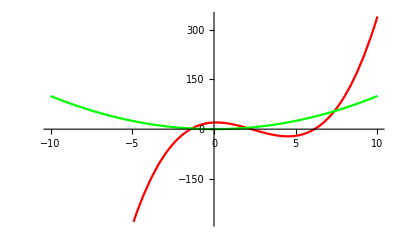

```mathematica
Plot[{f[x],g[x]},{x,-10,10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
```